```mathematica
d=0.12;y=0.2; y1=0.404;d=0.12; t=0.4; c=6.25;a1=0.00125; G1=0.00086; b=0.0004138*6/70; mu1=0.13;
f6[x_,n1_,U_]:=√(d^2+U^2+(a1*n1/x)+t^2-2*√((t^2+U^2)*(a1*n1/x)+U^2*d^2));
F5[x_,n1_,U]=(1/((y-f6[x,n1,U])^2+G1^2));
F6[x_,U_]=b*0.4*G1*Sum[F5[x,n1,U],{n1,0,100}]*(1/x);
F56[x_,n1_]=(1/((y1-f6[x,n1,0])^2+G1^2));
F66[x_]=b*0.4*G1*Sum[F56[x,n1],{n1,0,100}]*(1/x);
Plot[{F6[x,0.225]+4,F6[x,0.180]+2,F6[x,0.12],F6[x,0.14],4,2},{x,0,0.05},PlotRange->{0,6.5},PlotStyle->{{Thickness[0.003],Blue},{Thickness[0.003],Green},{Thickness[0.003],Black},{Thickness[0.003],Red,Dashed},{Thickness[0.003],Black},{Thickness[0.003],Black}},Epilog->{{Black,Text["U = 120  meV",{0.037,0.9},{-1,-1}]},{Black,Text["U = 140  meV",{0.037,1.3},{-1,-1}]},{Black,Text["U = 180  meV",{0.037,3},{-1,-1}]},{Black,Text["U = 225 meV",{0.037,5},{-1,-1}]}},FrameLabel->{Style["1/B, T^-1",10],Style["DOS, rel. units",10]},Frame->True]
```

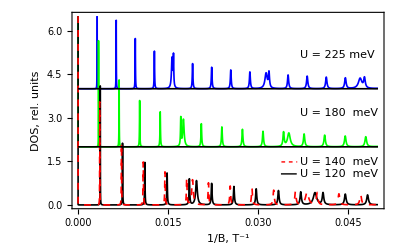

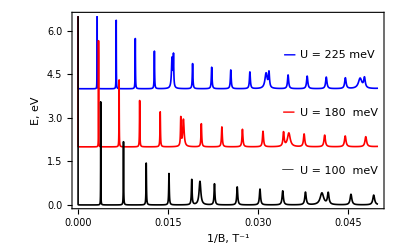

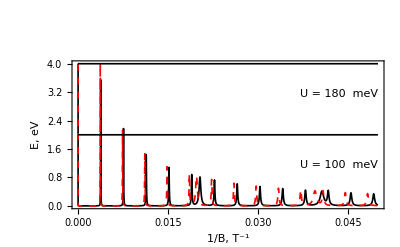

```mathematica
Plot[{F6[x,0.1],F6[x,0.120],4,2},{x,0,0.05},PlotRange->{0,4},PlotStyle->{{Thickness[0.003],Black},{Thickness[0.003],Red,Dashed},{Thickness[0.003],Black},{Thickness[0.003],Black},{Thickness[0.003],Black}},Epilog->{{Black,Text["U = 100  meV",{0.037,1},{-1,-1}]},{Black,Text["U = 180  meV",{0.037,3},{-1,-1}]},{Black,Text["U = 225 meV",{0.037,5},{-1,-1}]}},FrameLabel->{Style["1/B, T^-1",10],Style["E, eV",10]},Frame->True]
```

```mathematica
D6[x_,U_]:=√(d^2+U^2+(c*x)^2+t^2-2*√((t^2+U^2)*(c*x)^2+U^2*d^2));

Framed[Manipulate[Plot[{D6[x,U],0.403},{x,-0.15,0.15},PlotRange->{0.3,0.45}],{U,0,0.26},Alignment->{Right,Right},ContentSize->{400,400}],RoundingRadius->20]
```